```mathematica
goodgraph[graph_]:=Block[{vd=And@@Map[#>2&,VertexDegree[graph]]},Piecewise[{{Block[{vc=VertexConnectivity[graph]},Piecewise[{{Block[{ec=EdgeConnectivity[graph]},Piecewise[{{Block[{cyd=Length[FindCycle[graph,∞,3]]},Piecewise[{{True, cyd==3}, {False, cyd≠3}}]], ec>1}, {False, ec≤1}}]], vc>1}, {False, vc≤1}}]], vd}, {False, ¬vd}}]]
gedges[graph_,edges_]:=Block[{ged=(Length[EdgeList[graph]]≤edges)},Piecewise[{{goodgraph[graph], ged}, {False, ¬ged}}]]
```

```mathematica
rev[e_,dir_]:=Piecewise[{{e[[1]]->e[[2]], dir==0}, {e[[2]]->e[[1]], dir==1}}]
nthOriantation[g_,n0_,el_,len_]:=Block[{n=PadLeft[IntegerDigits[n0,2],len]},
Table[rev[el[[i]],n[[i]]],{i,1,len}]]
eq1[x_]:=Boole[x==1]
countOrientations[sofar_,b_]:=sofar+eq1[Length[ConnectedComponents[Graph[b]]]]

countStrongOrientations[graph_]:=Block[{el=EdgeList[graph]},
Block[{len=Length[el]},
Fold[countOrientations,0,Table[nthOriantation[graph,j,el,len],{j,1,2^len-1}]]]]
```

```mathematica
fold1Esc[sofar_,l_]:=Block[{g=Graph[l]},sofar+Boole[Fold[#1*#2&,1,VertexInDegree[g]*VertexOutDegree[g]]≠0]]
count1Esc[graph_]:=Block[{el=EdgeList[graph]},
Block[{len=Length[el]},
Fold[fold1Esc,0,Table[nthOriantation[graph,j,el,len],{j,1,2^len-1}]]]]
```

```mathematica
gg16=Select[GraphData[;;10],gedges[GraphData[#],16]&];
```

```mathematica
Length[gg16]
```

203

```mathematica
Monitor[Table[{gg16[[k]],count1Esc[GraphData[gg16[[k]]]],countStrongOrientations[GraphData[gg16[[k]]]]},{k,1,203}],{k,j}]
```

```mathematica
g1results={{{6,114},264,264},{{6,130},268,252},{{6,148},3936,3912},{{6,149},704,696},{{7,344},2040,2040},{{7,550},840,792},{{7,551},1812,1764},{{7,552},2060,1980},{{7,553},4328,4248},{{7,737},830,822},{{7,738},1964,1956},{{7,740},4480,4440},{{7,763},916,876},{{7,764},2050,2010},{{7,765},2044,2028},{{7,766},2238,2190},{{7,767},4884,4836},{{7,768},10748,10668},{{7,770},5078,4998},{{7,771},5528,5472},{{7,772},12148,12060},{{7,773},25824,25704},{{7,839},910,894},{{7,840},2238,2190},{{7,841},2232,2208},{{7,842},5324,5268},{{7,843},5542,5430},{{7,844},5072,5016},{{7,845},5536,5448},{{7,846},12156,12036},{{7,847},26800,26616},{{7,888},910,894},{{7,889},2232,2208},{{7,890},5318,5286},{{7,892},5542,5430},{{7,893},12156,12036},{{7,894},2456,2352},{{7,895},5524,5484},{{7,896},6042,5922},{{7,897},13244,13116},{{7,898},29196,28980},{{7,899},12620,12468},{{7,901},13762,13554},{{7,902},13744,13608},{{7,903},30284,30060},{{7,905},2438,2406},{{7,906},2436,2412},{{7,907},6024,5976},{{7,910},13728,13656},{{7,912},32988,32748},{{7,934},864,720},{{7,935},2016,1800},{{7,949},2084,1908},{{7,952},2272,2088},{{7,953},4936,4680},{{7,954},5584,5304},{{7,955},11776,11424},{{7,956},932,828},{{7,963},916,876},{{7,964},2244,2172},{{7,965},5336,5232},{{7,967},5556,5388},{{7,968},12176,11976},{{7,986},5560,5376},{{7,987},6068,5844},{{7,988},13288,12984},{{7,989},29248,28824},{{7,990},13796,13452},{{7,991},15032,14664},{{7,992},33064,32520},{{7,1001},27840,27480},{{7,1002},12644,12396},{{7,1003},12608,12504},{{7,1004},13764,13548},{{7,1005},30304,30000},{{7,1008},5536,5448},{{7,1009},5548,5412},{{7,1013},13256,13080},{{7,1015},31824,31504},{{7,1017},2464,2328},{{7,1018},2450,2370},{{7,1019},6056,5880},{{7,1020},14464,14192},{{7,1023},30328,29928},{{7,1025},13776,13512},{{7,1026},15020,14700},{{7,1027},33032,32616},{{7,1029},34288,33768},{{7,1030},34276,33804},{{7,1035},31424,31152},{{7,1037},31460,31044},{{"Antiprism",4},23168,21752},{{"Apollonian",2},11160,11040},{{"BiggestLittlePolygon",6},1732,1716},{{"BiggestLittlePolygon",8},21212,20100},{"BislitCube",3180,2964},{{"BlackBishop",{4,4}},2688,2448},{{"Circulant",{7,{1,2}}},6612,6388},{{"Complete",6},22400,22320},{{"CompleteBipartite",{3,4}},906,906},{{"CompleteBipartite",{3,5}},6510,6510},{{"CompleteBipartite",{4,4}},22874,22730},{{"CompleteTripartite",{1,3,3}},14414,14342},{{"Cone",{3,3}},1452,1452},{{"Cone",{3,4}},9492,9492},{{"Cone",{4,3}},34254,33870},{{"Cubic",{8,2}},464,384},{{"Cubic",{8,3}},456,408},{{"Cubic",{10,2}},2224,864},{{"Cubic",{10,3}},2168,1152},{{"Cubic",{10,4}},2208,1152},{{"Cubic",{10,5}},2144,1224},{{"Cubic",{10,6}},2088,1536},{{"Cubic",{10,7}},2096,1536},{{"Cubic",{10,8}},2056,1632},{{"Cubic",{10,9}},2072,1632},{{"Cubic",{10,10}},2064,1632},{{"Cubic",{10,11}},2040,1704},{{"Cubic",{10,12}},2112,1536},{{"Cubic",{10,13}},2032,1728},{{"Cubic",{10,14}},2022,1734},{{"Cubic",{10,16}},1992,1848},{{"Cubic",{10,18}},1984,1872},{"CubicalGraph",450,426},{{"Fan",{2,4}},706,690},{{"Fan",{2,5}},5550,5406},{{"Fan",{3,3}},642,642},{{"Fan",{3,4}},14994,14778},{{"Fan",{4,3}},4470,4470},{{"GeneralizedPrism",{3,3}},4304,3264},{{"HamiltonLaceable",{8,7}},1176,1152},{{"HamiltonLaceable",{8,8}},3142,3102},{{"HamiltonLaceable",{8,11}},8460,8388},{{"Harary",{3,7}},344,336},{{"Harary",{3,9}},1542,1422},{{"Heptahedral",2},352,312},{{"Heptahedral",4},1972,1932},{{"Heptahedral",5},2246,2166},{{"Heptahedral",6},4892,4812},{{"Heptahedral",7},346,330},{{"Heptahedral",8},832,816},{{"Heptahedral",9},1966,1950},{{"Heptahedral",10},2052,2004},{{"Heptahedral",11},2058,1986},{{"Heptahedral",12},2246,2166},{{"Heptahedral",13},4892,4812},{{"Heptahedral",15},11724,11580},{{"Heptahedral",16},5080,4992},{{"Heptahedral",18},918,870},{{"Heptahedral",20},2240,2184},{{"Heptahedral",21},924,852},{{"Heptahedral",22},2252,2148},{{"Heptahedral",23},5104,4920},{{"Heptahedral",25},924,852},{{"Heptahedral",26},2264,2112},{{"Heptahedral",27},5368,5136},{{"Heptahedral",28},5568,5352},{{"Heptahedral",29},12200,11904},{{"Heptahedral",30},2464,2328},{{"Heptahedral",31},6056,5880},{{"Heptahedral",34},13788,13476},{{"Hexahedral",3},266,258},{{"Hexahedral",4},644,636},{{"Hexahedral",5},1588,1572},{{"JohnsonSkeleton",3},4172,3660},{{"JohnsonSkeleton",8},11058,10314},{{"JohnsonSkeleton",12},204,204},{{"JohnsonSkeleton",13},15020,14700},{{"JohnsonSkeleton",14},8736,6936},{{"JohnsonSkeleton",26},3172,3012},{{"JohnsonSkeleton",49},2452,2364},{{"JohnsonSkeleton",63},4200,3552},{{"King",{2,3}},592,576},{{"King",{2,4}},16672,14112},{{"Lattice",{2,4}},23200,21128},{{"Matchstick",3},488,288},{{"MoebiusLadder",5},2006,1806},{"MoserSpindle",360,288},{"OctahedralGraph",1894,1862},{"PentatopeGraph",544,544},{"PetersenGraph",1968,1920},{{"Prism",3},104,96},{{"Prism",5},2008,1800},{{"Quartic",{7,1}},6604,6412},{{"Quartic",{8,1}},23128,21896},{{"Quartic",{8,4}},23086,22046},{{"Quartic",{8,5}},23012,22292},{{"Queen",{2,3}},4292,4260},{{"SelfComplementary",{8,5}},3280,2664},{{"SelfComplementary",{8,6}},3230,2814},{{"SelfComplementary",{8,10}},3180,2964},{"SelfDualGraph1",936,816},{"SelfDualGraph2",838,798},{"SelfDualGraph3",912,888},{"TetrahedralGraph",24,24},{{"Turan",{6,5}},9792,9744},{"UtilityGraph",102,102},{"WagnerGraph",448,432},{{"Wheel",5},78,78},{{"Wheel",6},240,240},{{"Wheel",7},726,726},{{"Wheel",8},2184,2184},{{"Wheel",9},6558,6558}};
```

```mathematica
g1results=Out[166];
```

```mathematica
g1eq=Map[First,Select[g1results,(#[[2]]==#[[3]])&]];
```

```mathematica
g1neq=Map[First,Select[g1results,(#[[2]]≠#[[3]])&]];
```

```mathematica
Map[GraphData[#,"PerfectMatching"]&,g1eq]
Map[GraphData[#,"PerfectMatching"]&,g1neq]
```

{True,False,False,False,True,False,True,False,False,False,True,True,False,True,False,True,False}

{True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,False,True,True,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,True,True,False,False,True,True,True,True,True,False,True,True,True,True,False,True,True,True,True,True,True,True,False,False,False,True,True}

```mathematica
Map[VertexDegree[GraphData[#]]&,g1eq]//Column
```

{3,3,3,4,3,4}
{3,3,3,3,5,4,5}
{4,4,4,3,3,3,3}
{5,5,5,3,3,3,3,3}
{5,5,5,3,3,3}
{6,6,6,3,3,3,3}
{4,5,4,3,3,3}
{5,6,5,3,3,3,3}
{3,3,4,4,4}
{4,4,4,4,4}
{3,3,3,3}
{3,3,3,3,3,3}
{3,3,3,3,4}
{3,3,3,3,3,5}
{3,3,3,3,3,3,6}
{3,3,3,3,3,3,3,7}
{3,3,3,3,3,3,3,3,8}

```mathematica
Map[PlanarGraphQ[GraphData[#]]&,g1eq]
```

{False,False,False,False,False,False,False,False,True,False,True,False,True,True,True,True,True}

```mathematica
density[graph_]:=Block[{v=Length[VertexList[graph]],e=Length[EdgeList[graph]]},(2e)/(v(v-1))]
```

```mathematica
Map[Min[VertexDegree[GraphData[#]]]&,g1eq]
Map[Min[VertexDegree[GraphData[#]]]&,g1neq]
```

{3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3}

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,3,3,3,3,4,3,3,3,4,3,3,4,4,4,4,3,3,4,3,3,3,3,3,4,5,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,4,3,3,3,4,3,3,3,4,4,4,4,4,3,3,3,3,3,3,4,3}

```mathematica
Sort[Map[Mean[VertexDegree[GraphData[#]]]&,g1eq]]//N
Sort[Map[Mean[VertexDegree[GraphData[#]]]&,g1neq]]//N
```

{3.,3.,3.2,3.33333,3.33333,3.42857,3.42857,3.5,3.55556,3.6,3.66667,3.71429,3.75,4.,4.,4.,4.28571}

{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.11111,3.14286,3.14286,3.14286,3.14286,3.25,3.33333,3.33333,3.33333,3.33333,3.33333,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.42857,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.55556,3.66667,3.66667,3.66667,3.66667,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.71429,3.75,3.75,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.33333,4.33333,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.57143,4.66667,5.}

```mathematica
Sort[Map[Max[VertexDegree[GraphData[#]]]-Min[VertexDegree[GraphData[#]]]&,g1eq]]
Sort[Map[Max[VertexDegree[GraphData[#]]]-Min[VertexDegree[GraphData[#]]]&,g1neq]]
```

{0,0,0,1,1,1,1,2,2,2,2,2,3,3,3,4,5}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
comp[f_]:={Map[f[GraphData[#]]&,g1eq],Map[f[GraphData[#]]&,g1neq]}
comps[f_]:={Sort[Map[f[GraphData[#]]&,g1eq]],Sort[Map[f[GraphData[#]]&,g1neq]]}
```

```mathematica
comp[VertexConnectivity]
```

{{3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3},{2,3,3,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,4,3,3,4,4,4,4,3,3,4,3,3,3,3,2,4,5,4,4,4,3,3,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,2,2,4,2,3,2,4,3,3,3,3,3,4,4,4,2,3,3,3,3,3,4,3}}

```mathematica
comp[EdgeConnectivity]
```

{{3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,3,3,3,3,4,3,3,3,4,3,3,4,4,4,4,3,3,4,3,3,3,3,3,4,5,4,4,4,3,3,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,4,2,3,3,4,3,3,3,4,4,4,4,4,3,3,3,3,3,3,4,3}}

```mathematica
comp[GroupOrder[GraphAutomorphismGroup[#]]&]
```

{{12,48,144,720,36,144,12,48,12,120,24,72,8,10,12,14,16},{16,12,8,4,4,8,8,2,4,4,4,2,4,2,2,4,4,8,8,24,2,1,2,2,2,2,1,1,4,4,2,8,2,4,4,4,2,2,4,4,4,4,4,8,24,12,36,12,4,8,4,4,4,24,24,4,4,2,4,2,4,4,2,2,4,4,16,16,8,2,8,2,2,2,2,2,20,4,2,2,12,2,1,2,2,4,4,12,4,16,6,4,2,8,8,14,720,1152,72,48,4,12,16,4,8,16,2,4,4,8,12,6,6,2,48,4,8,48,4,4,12,12,12,16,72,4,2,2,2,2,2,4,2,4,1,2,1,1,4,2,1,2,2,2,2,2,1,4,1,2,2,2,6,2,2,4,6,8,20,12,8,4,6,16,32,48,16,20,8,48,120,12,20,48,12,4,16,16,32,2,8,6,1,6,48,16}}

```mathematica
comps[Boole[EulerianGraphQ[#]]&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
comps[Boole[BipartiteGraphQ[#]]&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1}}

```mathematica
comps[Boole[HamiltonianGraphQ[#]]&]
```

{{0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
comps[N[VertexCount[#]/Min[VertexDegree[#]]]&]
```

{{1.25,1.33333,1.66667,1.66667,2.,2.,2.,2.,2.,2.33333,2.33333,2.33333,2.33333,2.33333,2.66667,2.66667,3.},{1.2,1.5,1.5,1.5,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,1.75,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.33333,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,2.66667,3.,3.,3.,3.,3.,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333,3.33333}}

```mathematica
comps[GraphRadius]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3}}

```mathematica
comps[GraphDiameter]
```

{{1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4}}

```mathematica
comps[GraphDensity]//N
```

{{0.444444,0.5,0.535714,0.571429,0.571429,0.6,0.619048,0.666667,0.666667,0.666667,0.714286,0.733333,0.8,0.8,0.9,1.,1.},{0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.388889,0.416667,0.416667,0.416667,0.428571,0.428571,0.428571,0.428571,0.428571,0.444444,0.464286,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.52381,0.52381,0.52381,0.52381,0.535714,0.535714,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.571429,0.6,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.619048,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.714286,0.733333,0.733333,0.733333,0.733333,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.761905,0.8,0.8,0.8,0.866667,0.866667,0.933333,1.}}

```mathematica
comps[Max[ClosenessCentrality[#]]&]
```

{{0.714286,0.75,0.777778,0.833333,0.857143,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.529412,0.529412,0.529412,0.529412,0.529412,0.529412,0.5625,0.5625,0.5625,0.5625,0.5625,0.5625,0.583333,0.583333,0.6,0.6,0.6,0.6,0.6,0.6,0.615385,0.636364,0.636364,0.636364,0.666667,0.666667,0.666667,0.666667,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.714286,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.777778,0.777778,0.777778,0.833333,0.833333,0.833333,0.833333,0.833333,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
comps[Min[Eigenvalues[AdjacencyMatrix[#]]]&]//N
```

{{-3.,-2.,-2.,-2.,-1.,-1.,-3.4641,-3.87298,-1.82843,-1.61803,-1.64575,-2.16228,-2.60555,-2.91852,-2.48361,-3.17554,-2.71774},{-4.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-1.,-1.73205,-2.23607,-2.23607,-1.82843,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.73205,-2.73205,-2.73205,-2.73205,-2.61803,-2.61803,-2.61803,-3.23607,-2.31662,-3.30278,-2.60555,-3.56155,-2.56155,-2.56155,-2.56155,-2.56155,-3.79129,-2.37228,-2.54138,-1.70156,-1.70156,-2.84224,-2.50366,-1.90952,-2.3478,-2.48535,-1.80354,-2.88341,-2.6737,-1.75252,-1.6874,-2.58687,-2.26354,-1.85577,-2.40198,-2.83692,-3.25417,-2.23073,-2.70928,-1.80194,-2.47283,-2.81361,-2.24698,-2.24698,-2.24698,-2.24698,-2.24698,-3.07665,-2.51355,-3.06978,-2.59342,-2.56442,-2.55776,-2.24177,-2.24325,-2.50455,-2.48675,-2.14463,-2.95186,-1.80651,-2.17905,-2.72607,-2.68873,-2.48298,-2.50293,-2.66067,-2.18477,-2.22736,-2.53603,-2.26676,-2.29292,-2.52383,-2.83436,-2.59615,-2.59615,-2.51144,-2.52346,-2.62722,-2.58194,-2.38084,-1.83756,-2.193,-2.19066,-1.88773,-2.43974,-2.26209,-2.37859,-2.17948,-2.23081,-2.23171,-2.29022,-2.20156,-2.40831,-2.38408,-2.76865,-2.31789,-2.56991,-2.75087,-2.24061,-2.24061,-2.2787,-2.27221,-2.78908,-1.82337,-2.33444,-2.665,-2.24633,-2.48011,-2.45619,-2.66695,-2.71861,-2.4718,-2.51753,-2.84194,-2.79427,-2.54535,-2.21186,-2.42979,-2.48981,-2.30924,-2.49515,-2.20406,-2.23717,-2.29586,-2.1863,-2.2337,-2.28497,-2.25829,-2.39651,-2.20832}}

```mathematica
First[FindShortestTour[GraphData[g1eq[[1]]]]]
```

6

```mathematica
comps[First[FindShortestTour[#]]&]
```

First::nofirst: {} has a length of zero and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

{{4,5,5,5,6,6,6,6,6,7,8,9,First[{}],First[{}],First[{}],First[{}],First[{}]},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,First[{}]}}

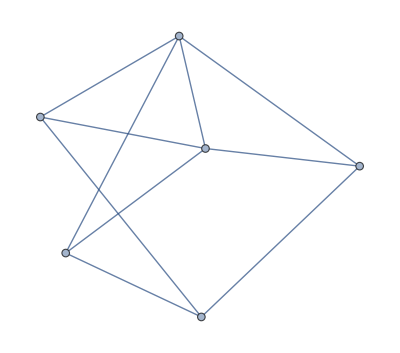
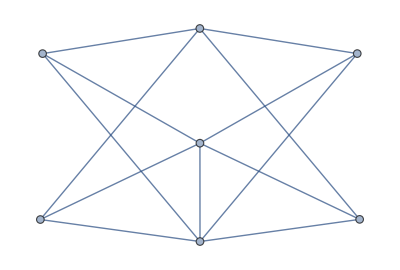
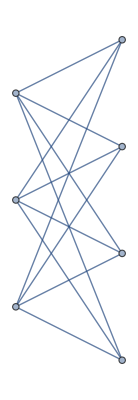
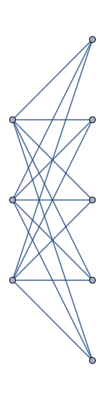
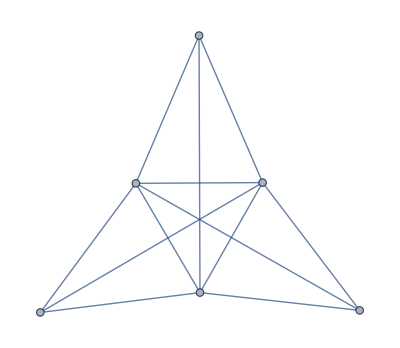
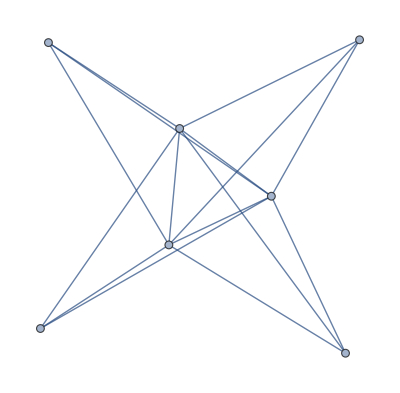
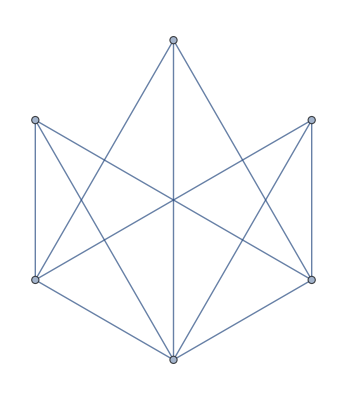
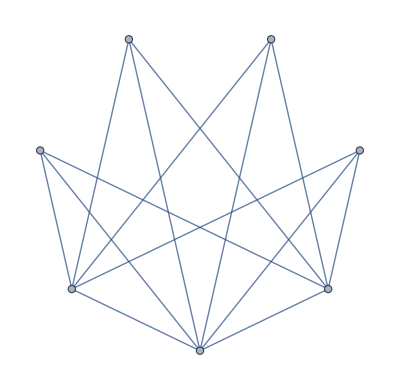

```mathematica
Map[GraphData,g1eq]
```

```mathematica
Map[GraphData,{{6,114},{7,344},{"CompleteBipartite",{3,4}},{"CompleteBipartite",{3,5}},{"Cone",{3,3}},{"Cone",{3,4}},{"Fan",{3,3}},{"Fan",{4,3}},{"JohnsonSkeleton",12},"PentatopeGraph","UtilityGraph"}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

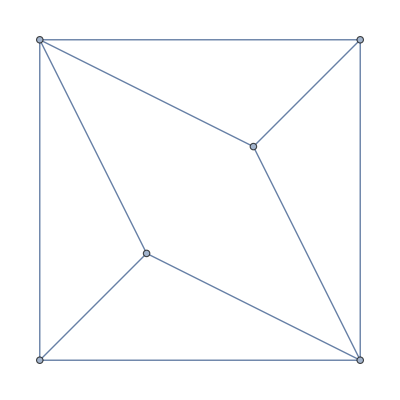
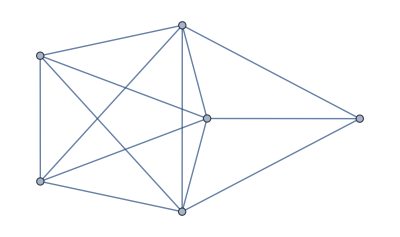
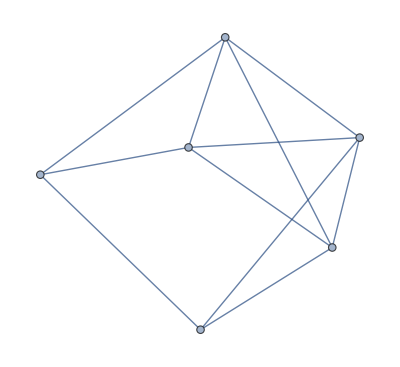
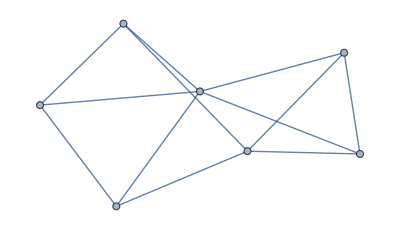
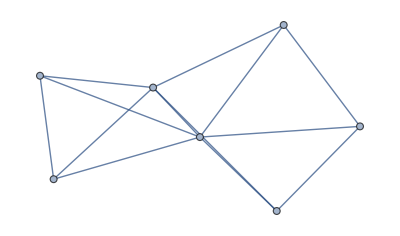
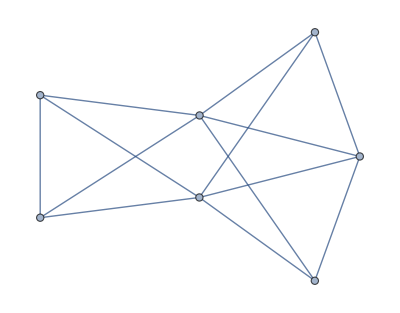
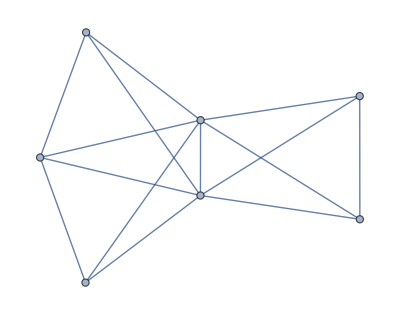
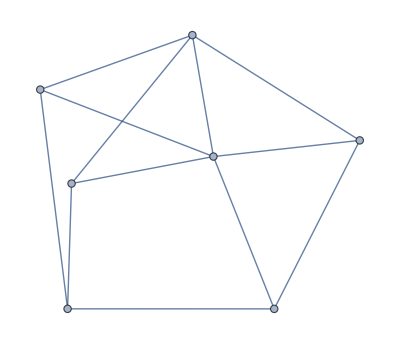
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[GraphData,g1neq]
```

```mathematica
comps[Boole[2*GraphDiameter[#]+1==Min[Map[Length,FindCycle[#,∞,All]]]]&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}